```mathematica
ConfigureMaTeX[
"pdfLaTeX"->"C:\\Users\\Nanoplasmonics\\AppData\\Local\\Programs\\MiKTeX\\miktex\\bin\\x64\\pdflatex.exe","Ghostscript"->"C:\\Program Files\\gs\\gs10.05.1\\bin\\gswin64c.exe"
]
```

ConfigureMaTeX[pdfLaTeX→C:\Users\Nanoplasmonics\AppData\Local\Programs\MiKTeX\miktex\bin\x64\pdflatex.exe,Ghostscript→C:\Program Files\gs\gs10.05.1\bin\gswin64c.exe]

```mathematica
Needs["MaTeX`"]
```

ConfigureMaTeX::shdw: Symbol ConfigureMaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

```mathematica
h c/1200
```

1.03392

```mathematica
lambdamin=250;
lambdamax=1300;
energyTicksMajor={1.03,1.24,1.55,2.07,3.1};
```

```mathematica
(*Esta función grafica el ajuste de Lorentz de la parte imaginaria de la función dieléctrica y los datos experimentales. Recibe funciones*)
plotLorentzFit[lorentz_,exp_,energyTicksMajor_,lambdamin_,lambdamax_]:=Module[{majorTicks},(*Calcular ticks mayores en energía*)majorTicks=Module[{positions},positions=h c/#&/@energyTicksMajor;
Transpose[{positions,energyTicksMajor}]];
(*Graficar*)Plot[{lorentz[λ],Style[exp[λ],Red,Dashed]},{λ,lambdamin,lambdamax},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],FrameLabel->{{Style[MaTeX["\mbox{Im}\{\varepsilon(\omega)\}"],Magnification->1.6],None},{Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.6],Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"Latin Modern Roman 10"},FrameTicks->{{Automatic,None},{Automatic,majorTicks}},PlotRange->All,PlotLegends->Placed[SwatchLegend[{"Ajuste de Lorentz","Datos sin ajustar"},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.5,0.65}]
,ImagePadding->{{70,10},{60,50}}]]

(*Esta función grafica la parte real  de la función dieléctrica obtenidos de KK.Recibe una lista de puntos*)
plotDielectricFunctionKKRe[parteRe_,energyTicksMajor_,lambdamin_,lambdamax_]:=Module[{majorTicks},(*Calcular ticks mayores en energía*)majorTicks=Module[{positions},positions=h c/#&/@energyTicksMajor;
Transpose[{positions,energyTicksMajor}]];
(*Graficar*)Plot[{Style[parteRe[λ],Blue]},{λ,lambdamin,lambdamax},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],FrameLabel->{{Style[MaTeX["\mbox{Re}\{\varepsilon(\omega)\}"],Magnification->1.6],None},{Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.6],Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"Latin Modern Roman 10"},FrameTicks->{{Automatic,None},{Automatic,majorTicks}},PlotRange->All,ImagePadding->{{70,10},{60,50}}]]

(*Esta función grafica la parte imaginaria  de la función dieléctrica obtenidos de KK*)
plotDielectricFunctionKKIm[parteIm_,energyTicksMajor_,lambdamin_,lambdamax_]:=Module[{majorTicks},(*Calcular ticks mayores en energía*)majorTicks=Module[{positions},positions=h c/#&/@energyTicksMajor;
Transpose[{positions,energyTicksMajor}]];
(*Graficar*)Plot[{Style[parteIm[λ],Red]},{λ,lambdamin,lambdamax},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],FrameLabel->{{Style[MaTeX["\mbox{Im}\{\varepsilon(\omega)\}"],Magnification->1.6],None},{Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.6],Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"Latin Modern Roman 10"},FrameTicks->{{Automatic,None},{Automatic,majorTicks}},PlotRange->All,ImagePadding->{{70,10},{60,50}}]]

(*Esta función grafica el ajuste de Lorentz de la parte imaginaria de la función dieléctrica y los datos experimentales. Recibe funciones*)
plotDielectricFunctionDifConcentrationsIm[qlist_List,energyTicksMajor_,lambdamin_,lambdamax_]:=Module[{majorTicks},(*Calcular ticks mayores en energía*)majorTicks=Module[{positions},positions=h c/#&/@energyTicksMajor;
Transpose[{positions,energyTicksMajor}]];
(*Graficar*)Plot[Evaluate@Table[ql[λ],{ql,qlist}],{λ,lambdamin,lambdamax},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],FrameLabel->{{Style[MaTeX["\mbox{Im}\{\varepsilon(\omega)\}"],Magnification->1.6],None},{Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.6],Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"Latin Modern Roman 10"},FrameTicks->{{Automatic,None},{Automatic,majorTicks}},PlotRange->All,PlotLegends->Placed[SwatchLegend[{Style["15.3",Magnification->1.2],Style["28.7",Magnification->1.2],Style["30.6",Magnification->1.2]},LegendMarkerSize->{15,5},LegendMargins->0,LegendLayout->{"Column",1},LegendLabel->Style["Concentración [g/dL]",FontFamily->"Latin Modern Roman 10",Magnification->1.2]],{0.7,0.65}]
,ImagePadding->{{70,10},{60,50}}]]

(*Esta función grafica el ajuste de Lorentz de la parte imaginaria de la función dieléctrica y los datos experimentales. Recibe funciones*)
plotDielectricFunctionDifConcentrationsRe[qlist_List,energyTicksMajor_,lambdamin_,lambdamax_]:=Module[{majorTicks},(*Calcular ticks mayores en energía*)majorTicks=Module[{positions},positions=h c/#&/@energyTicksMajor;
Transpose[{positions,energyTicksMajor}]];
(*Graficar*)Plot[Evaluate@Table[ql[λ],{ql,qlist}],{λ,lambdamin,lambdamax},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],FrameLabel->{{Style[MaTeX["\mbox{Re}\{\varepsilon(\omega)\}"],Magnification->1.6],None},{Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.6],Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"Latin Modern Roman 10"},FrameTicks->{{Automatic,None},{Automatic,majorTicks}},PlotRange->All,PlotLegends->Placed[SwatchLegend[{Style["15.3",Magnification->1.2],Style["28.7",Magnification->1.2],Style["30.6",Magnification->1.2]},LegendMarkerSize->{15,5},LegendMargins->0,LegendLayout->{"Column",2},LegendLabel->Style["Concentración [g/dL]",FontFamily->"Latin Modern Roman 10",Magnification->1.2]],{0.7,0.25}]
,ImagePadding->{{70,10},{60,50}}]]
```

InterpolatingFunction::dmval: Input value {4.99968} lies outside the range of data in the interpolating function. Extrapolation will be used.

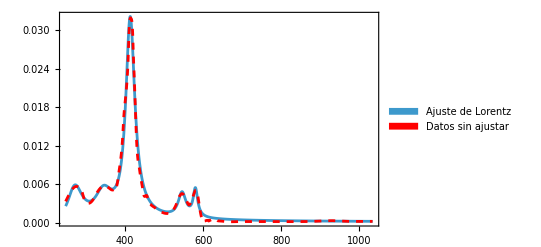

```mathematica
fit282[lambda_]:=fit28[h c/lambda]
eps282[lambda_]:=eps28[h c/lambda]
energyTicksMajor28={  1.24,1.55,2.07,3.1};
plotLorentzFit[fit282,eps282,energyTicksMajor28,h c/5,h c/1.2]
```

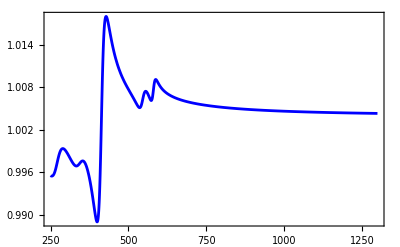

```mathematica
lambdas=Range[200,800,0.01];
parteRe281=Interpolation[Transpose[{omega,eps28KK[[1]]}]];
parteRe282[lambda_]:=parteRe281[h c/lambda];
plotDielectricFunctionKKRe[parteRe282,energyTicksMajor,lambdamin,lambdamax]
```

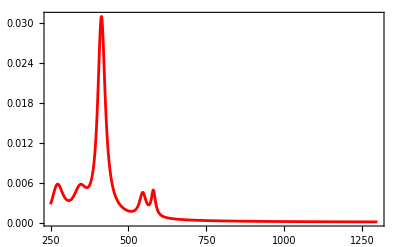

```mathematica
parteIm281=Interpolation[Transpose[{omega,eps28KK[[2]]}]];
parteIm282[lambda_]:=parteIm281[h c/lambda];
plotDielectricFunctionKKIm[parteIm282,energyTicksMajor,lambdamin,lambdamax]
```

InterpolatingFunction::dmval: Input value {4.99986} lies outside the range of data in the interpolating function. Extrapolation will be used.

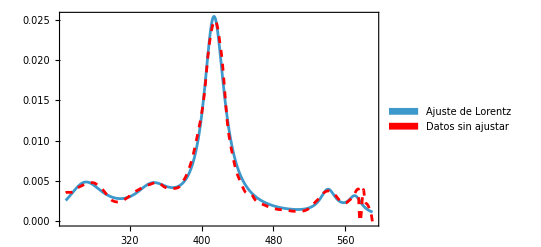

```mathematica
fit152[lambda_]:=fit15[h c/lambda]
eps152[lambda_]:=eps15[h c/lambda]
energyTicksMajor15={2.26,2.48,2.76,3.1,3.55,4.14,5};
plotLorentzFit[fit152,eps152,energyTicksMajor15,h c/5,h c/2.1]
```

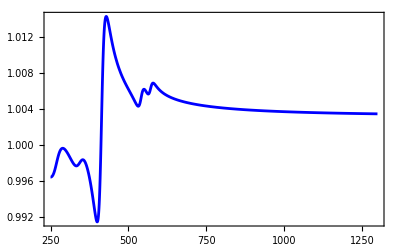

```mathematica
lambdas=Range[200,800,0.01];
parteRe151=Interpolation[Transpose[{omega,eps15KK[[1]]}]];
parteRe152[lambda_]:=parteRe151[h c/lambda];
plotDielectricFunctionKKRe[parteRe152,energyTicksMajor,lambdamin,lambdamax]
```

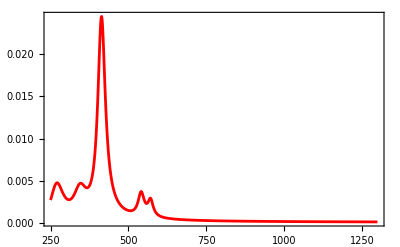

```mathematica
parteIm151=Interpolation[Transpose[{omega,eps15KK[[2]]}]];
parteIm152[lambda_]:=parteIm151[h c/lambda];
plotDielectricFunctionKKIm[parteIm152,energyTicksMajor,lambdamin,lambdamax]
```

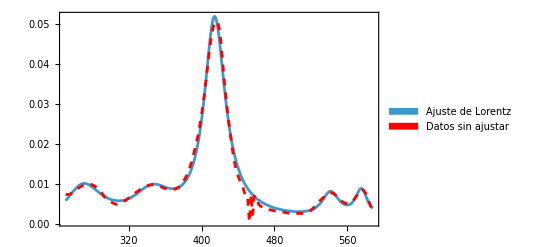

```mathematica
fit302[lambda_]:=fit30[h c/lambda]
eps302[lambda_]:=eps30[h c/lambda]
energyTicksMajor30={2.26,2.48,2.76,3.1,3.55,4.14,5};
plotLorentzFit[fit302,eps302,energyTicksMajor30,h c/4.95,h c/2.11]
```

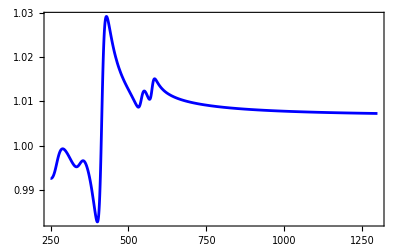

```mathematica
parteRe301=Interpolation[Transpose[{omega,eps30KK[[1]]}]];
parteRe302[lambda_]:=parteRe301[h c/lambda];
plotDielectricFunctionKKRe[parteRe302,energyTicksMajor,lambdamin,lambdamax]
```

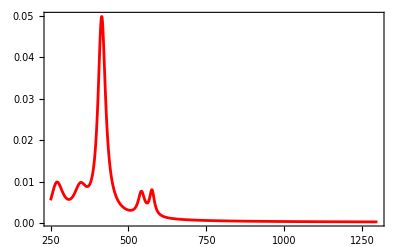

```mathematica
parteIm301=Interpolation[Transpose[{omega,eps30KK[[2]]}]];
parteIm302[lambda_]:=parteIm301[h c/lambda];
plotDielectricFunctionKKIm[parteIm302,energyTicksMajor,lambdamin,lambdamax]
```

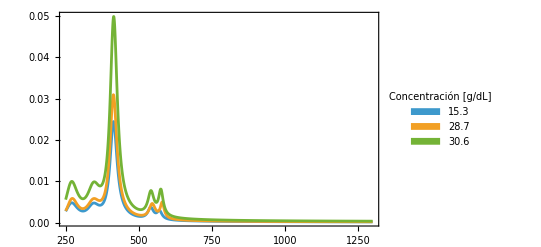

```mathematica
plotDielectricFunctionDifConcentrationsIm[{parteIm152,parteIm282,parteIm302},energyTicksMajor,lambdamin,lambdamax]
```

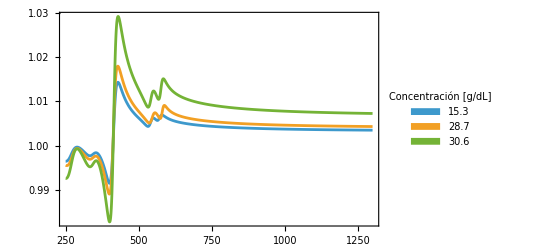

```mathematica
plotDielectricFunctionDifConcentrationsRe[{parteRe152,parteRe282,parteRe302},energyTicksMajor,lambdamin,lambdamax]
```

```mathematica
h c/1000
```

1.2407

InterpolatingFunction::dmval: Input value {3.49985} lies outside the range of data in the interpolating function. Extrapolation will be used.

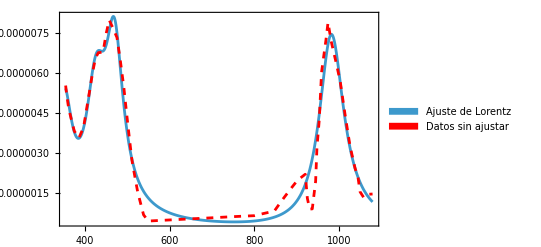

```mathematica
fitPlasma2[lambda_]:=fitPlasma[h c/lambda]
epsPlasma2[lambda_]:=epsPlasma[h c/lambda]
energyTicksMajorPlasma={  1.24,1.38,1.55,1.77,2.07,2.48,3.1};
plotLorentzFit[fitPlasma2,epsPlasma2,energyTicksMajorPlasma,h c/3.5,h c/1.15]
```

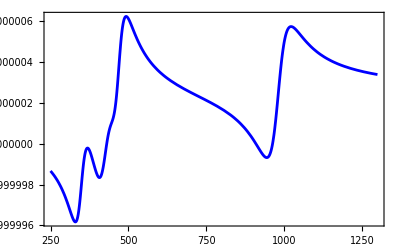

```mathematica
parteRePlasma1=Interpolation[Transpose[{omega,epsPlasmaKK[[1]]}]];
parteRePlasma2[lambda_]:=parteRePlasma1[h c/lambda];
plotDielectricFunctionKKRe[parteRePlasma2,energyTicksMajor,lambdamin,lambdamax]
```

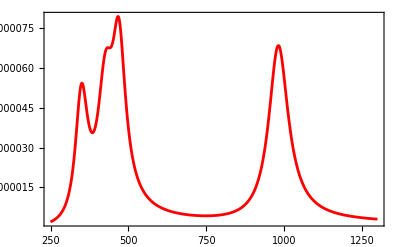

```mathematica
parteImPlasma1=Interpolation[Transpose[{omega,epsPlasmaKK[[2]]}]];
parteImPlasma2[lambda_]:=parteImPlasma1[h c/lambda];
plotDielectricFunctionKKIm[parteImPlasma2,energyTicksMajor,lambdamin,lambdamax]
```